```mathematica
VectorPlot[{y,-x+0.1x^3},{x,-6,6},{y,-6,6},PlotLegends->Automatic,AspectRatio->0.8,Frame->True]//Rasterize
```

-Graphics-

```mathematica
Animate[VectorPlot[{y,-x+0.1x^3+3Sin[2Pi*t]},{x,-6,6},{y,-6,6},PlotLegends->Automatic,AspectRatio->0.8,Frame->True],{t,0,3}]
```

```mathematica
VectorPlot[{y,-Sin[x]},{x,-2Pi,2Pi},{y,-3,3},FrameLabel->{"θ","ω"},PlotLegends->Automatic,AspectRatio->0.8,Frame->True]//Rasterize
```

-Graphics-

```mathematica
plot=StreamPlot[{y,-Sin[x]},{x,-Pi,Pi},{y,-2,2},Frame->None,Epilog->{PointSize->Large,Point[{{0,0},{π,0},{-π,0}}]},StreamPoints->Fine,AspectRatio->0.8];
Show[First[Normal@plot]/.  a_Arrow:>(a/. {x_Real,y_Real}:>{Cos[x],Sin[x],y})//Graphics3D,Graphics3D@{Opacity@.7,LightBlue,Cylinder[{{0,0,-2},{0,0,2}}]}]
```

-Graphics3D-

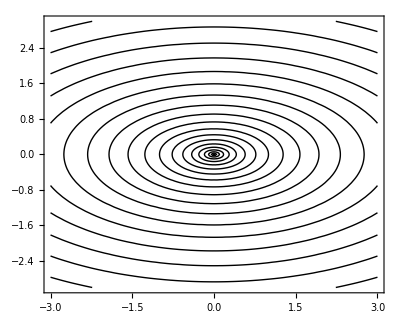

```mathematica
ContourPlot[x^2+3y^2,{x,-3,3},{y,-3,3},ContourShading->None,Contours->Table[i^5,{i,0,5,0.1}],AspectRatio->0.8]
```

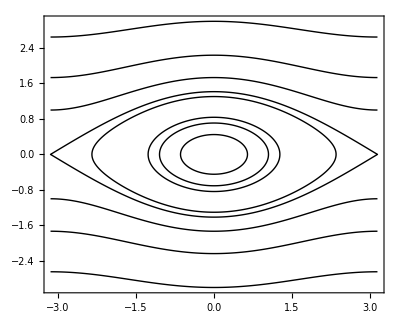

```mathematica
ContourPlot[y^2-Cos[x],{x,-Pi,Pi},{y,-3,3},ContourShading->None,Contours->{-1,1,0.7,-0.3,-0.8,-0.5,2,4,8},AspectRatio->0.8,PlotPoints->200]
```

```mathematica
(*参数*)σ=10;
ρ=28;
β=8/3;

(*洛伦兹系统*)
eqs={x'[t]==σ (y[t]-x[t]),y'[t]==x[t] (ρ-z[t])-y[t],z'[t]==x[t] y[t]-β z[t]};

(*初值*)
ics={x[0]==1,y[0]==1,z[0]==1};

(*数值求解*)
sol=NDSolve[Join[eqs,ics],{x,y,z},{t,0,50}];
ParametricPlot3D[Evaluate[{x[t],y[t],z[t]}/. sol],{t,10,50},PlotRange->All,AxesLabel->{"x","y","z"},BoxRatios->{1,1,1},PlotStyle->{Thick,Blue},PlotPoints->400]
```

-Graphics3D-

```mathematica
plot=StreamPlot[{1,-y+0.1 y^3+Sin[x]},{x,-Pi,Pi},{y,-2,2},Frame->None,Epilog->{PointSize->Large,Point[{{0,0},{π,0},{-π,0}}]},StreamPoints->Fine,AspectRatio->0.8];
Show[First[Normal@plot]/.  a_Arrow:>(a/. {x_Real,y_Real}:>{Cos[x],Sin[x],y})//Graphics3D,Graphics3D@{Opacity@.7,LightBlue,Cylinder[{{0,0,-2},{0,0,2}}]},Graphics3D[{Red,Thickness[0.01],Line[{{Cos[0],Sin[0],-2},{Cos[0],Sin[0],2}}]}],Boxed->False]
```

-Graphics3D-

```mathematica
R=2;
w=0.6;

mobius[{s_,x_}]:={(R+x Cos[s/2]) Cos[s],(R+x Cos[s/2]) Sin[s],x Sin[s/2]};
k=0.5;

vf={1,-k x};

plot2D=StreamPlot[vf,{s,-Pi,Pi},{x,-w,w},StreamPoints->Fine,Frame->False,AspectRatio->0.5];
Show[First[Normal@plot]/.  a_Arrow:>(a/. {y_Real,x_Real}:>{(R+x Cos[y/2]) Cos[y],(R+x Cos[y/2]) Sin[y],x Sin[y/2]})//Graphics3D,ParametricPlot3D[mobius[{s,x}],{s,-Pi,Pi},{x,-4w,4w},MeshStyle->None],Boxed->False]
```

-Graphics3D-